### Start choosing the example:

```mathematica
t=8;
beta = 0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x]
```

Log[x]

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/MFGraphs.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1},{4,U2}},Switching Costs→{{1,2,3,S1},{1,2,4,S2},{3,2,1,S3},{3,2,4,S4},{4,2,1,S5},{4,2,3,S6}}|>

DataToEquations: Triangle inequalities for switching costs: {True,True,True,True,True,True}
DataToEquations: Reduced: True

The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.04655 seconds to reduce with NewReduce!

DataToEquations: After NewReduce, the system is:
j1146==0&&jt1159==0&&u1168==3&&u1169==1&&-2≤u1170≤11
and the rules are:
<|j1149→1,u1177→0,u1178→31,j1144→1,j1145→1-j1146,j1147→1-j1146,j1148→j1146,j1150→0,j1151→0,j1152→0,j1153→0,j1154→0,j1155→0,jt1156→0,jt1157→1,jt1158→1-jt1159,jt1160→-j1146+jt1159,jt1161→j1146-jt1159,jt1162→j1146-jt1159,jt1163→-j1146+jt1159,jt1164→1-j1146,jt1165→0,jt1166→j1146,jt1167→0,u1171→0,u1172→31,u1174→-1+u1168,u1175→-1+j1146+u1169,u1176→-j1146+u1170,u1179→u1168,u1173→u1168|>

DataToEquations: Mixed system:

DataToEquations: Possible multiple solutions 
{-2≤u1170≤11,<|j1149→1,u1177→0,u1178→31,j1144→1,j1145→1-0,j1147→1-0,j1148→0,j1150→0,j1151→0,j1152→0,j1153→0,j1154→0,j1155→0,jt1156→0,jt1157→1,jt1158→1-0,jt1160→-0+0,jt1161→0-0,jt1162→0-0,jt1163→-0+0,jt1164→1-0,jt1165→0,jt1166→0,jt1167→0,u1171→0,u1172→31,u1174→-1+3,u1175→-1+0+1,u1176→-0+u1170,u1179→3,u1173→3,j1146→0,jt1159→0,u1168→3,u1169→1|>}

DataToEquations: Something went wrong, check the data.

DataToEquations: Done.

{0.06741,Null}

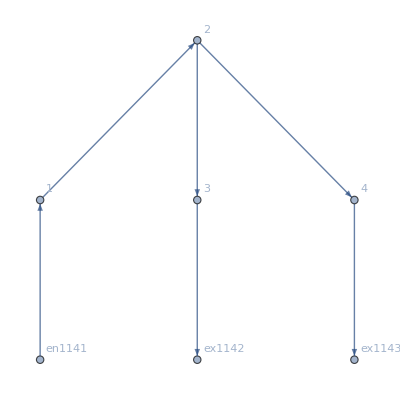

current: <|{1,1->2}→0,{1,en1141->1}→1,{2,1->2}→1,{2,2->3}→0,{2,2->4}→0,{3,2->3}→1,{3,3->ex1142}→0,{4,2->4}→0,{4,4->ex1143}→0,{en1141,en1141->1}→0,{ex1142,3->ex1142}→1,{ex1143,4->ex1143}→0|>

transition: <|{1,1->2,en1141->1}→0,{1,en1141->1,1->2}→1,{2,1->2,2->3}→1,{2,1->2,2->4}→0,{2,2->3,1->2}→0,{2,2->3,2->4}→0,{2,2->4,1->2}→0,{2,2->4,2->3}→0,{3,2->3,3->ex1142}→1,{3,3->ex1142,2->3}→0,{4,2->4,4->ex1143}→0,{4,4->ex1143,2->4}→0|>

value: <|{1,1->2}→3,{1,en1141->1}→3,{2,1->2}→2,{2,2->3}→1,{2,2->4}→u1170,{3,2->3}→0,{3,3->ex1142}→0,{4,2->4}→u1170,{4,4->ex1143}→31,{en1141,en1141->1}→3,{ex1142,3->ex1142}→0,{ex1143,4->ex1143}→31|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->1,U1->(*at vertex 3*)0,U2->(*at vertex 4*)31(*, S1->1,S2->2,S3->1,S4->1,S5->2,S6->1*),S1->(*S124*)1,S2->(*S123*)4,S3->3,S4->3,S5->9,S6->10}];//Timing
MFGEquations["FG"]
Print["current: ", MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort]
Print["transition: ", MFGEquations["jtvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort]
Print["value: ", MFGEquations["uvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort]
```

#### In the next example, it looks like we may choose one of the values for the value function. One of the extremes should be the consistent choice.

```mathematica
MFGEquations=DataToEquations[Data/.{I1->1,U1->(*at vertex 3*)0,U2->(*at vertex 4*)31,S1->1,S2->4,S3->3,S4->5,S5->3,S6->0}];//Timing
Print["current: ", MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort]
Print["transition: ", MFGEquations["jtvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort]
Print["value: ", MFGEquations["uvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort]
```

DataToEquations: Triangle inequalities for switching costs: {True,True,True,True,True,True}
DataToEquations: Reduced: True

The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.047025 seconds to reduce with NewReduce!

DataToEquations: After NewReduce, the system is:
j912==0&&jt925==0&&u934==3&&u935==1&&-2≤u936≤1
and the rules are:
<|j915→1,u943→0,u944→31,j910→1,j911→1-j912,j913→1-j912,j914→j912,j916→0,j917→0,j918→0,j919→0,j920→0,j921→0,jt922→0,jt923→1,jt924→1-jt925,jt926→-j912+jt925,jt927→j912-jt925,jt928→j912-jt925,jt929→-j912+jt925,jt930→1-j912,jt931→0,jt932→j912,jt933→0,u937→0,u938→31,u940→-1+u934,u941→-1+j912+u935,u942→-j912+u936,u945→u934,u939→u934|>

DataToEquations: Mixed system:

DataToEquations: Possible multiple solutions 
{-2≤u936≤1,<|j915→1,u943→0,u944→31,j910→1,j911→1-0,j913→1-0,j914→0,j916→0,j917→0,j918→0,j919→0,j920→0,j921→0,jt922→0,jt923→1,jt924→1-0,jt926→-0+0,jt927→0-0,jt928→0-0,jt929→-0+0,jt930→1-0,jt931→0,jt932→0,jt933→0,u937→0,u938→31,u940→-1+3,u941→-1+0+1,u942→-0+u936,u945→3,u939→3,j912→0,jt925→0,u934→3,u935→1|>}

DataToEquations: Something went wrong, check the data.

DataToEquations: Done.

{0.068459,Null}

current: <|{1,1->2}→0,{1,en907->1}→1,{2,1->2}→1,{2,2->3}→0,{2,2->4}→0,{3,2->3}→1,{3,3->ex908}→0,{4,2->4}→0,{4,4->ex909}→0,{en907,en907->1}→0,{ex908,3->ex908}→1,{ex909,4->ex909}→0|>

transition: <|{1,1->2,en907->1}→0,{1,en907->1,1->2}→1,{2,1->2,2->3}→1,{2,1->2,2->4}→0,{2,2->3,1->2}→0,{2,2->3,2->4}→0,{2,2->4,1->2}→0,{2,2->4,2->3}→0,{3,2->3,3->ex908}→1,{3,3->ex908,2->3}→0,{4,2->4,4->ex909}→0,{4,4->ex909,2->4}→0|>

value: <|{1,1->2}→3,{1,en907->1}→3,{2,1->2}→2,{2,2->3}→1,{2,2->4}→u936,{3,2->3}→0,{3,3->ex908}→0,{4,2->4}→u936,{4,4->ex909}→31,{en907,en907->1}→3,{ex908,3->ex908}→0,{ex909,4->ex909}→31|>

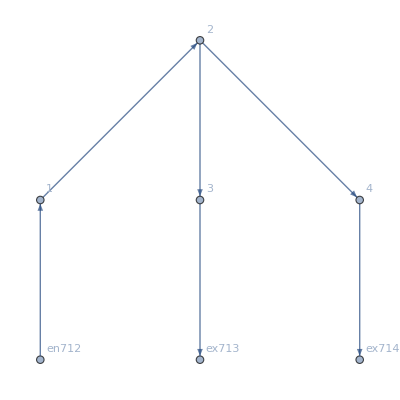

```mathematica
MFGEquations["FG"]
```

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 8.88178×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 8.88178×10^-16

<|j287→1,j288→1.,j289→0.,j290→1.,j291→0.,j292→1,j293→0,j294→0,j295→0,j296→0,j297→0,j298→0,jt299→0,jt300→1,jt301→1.,jt302→0.,jt303→0,jt304→0,jt305→0,jt306→0,jt307→1.,jt308→0,jt309→0.,jt310→0,u311→11.4115,u312→0.705756,u313→0.705756,u314→0,u315→31,u316→11.4115,u317→10.7058,u318→0.,u319→0.705756,u320→0,u321→31,u322→11.4115|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.11022×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.11022×10^-16

<|j287→1,j288→1.,j289→0.,j290→1.,j291→0.,j292→1,j293→0,j294→0,j295→0,j296→0,j297→0,j298→0,jt299→0,jt300→1,jt301→1.,jt302→0.,jt303→0,jt304→0,jt305→0,jt306→0,jt307→1.,jt308→0,jt309→0.,jt310→0,u311→11.4537,u312→0.72685,u313→0.72685,u314→0,u315→31,u316→11.4537,u317→10.7268,u318→0.,u319→0.72685,u320→0,u321→31,u322→11.4537|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.55112×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.55112×10^-16

<|j287→1,j288→1.,j289→0.,j290→1.,j291→0.,j292→1,j293→0,j294→0,j295→0,j296→0,j297→0,j298→0,jt299→0,jt300→1,jt301→1.,jt302→0.,jt303→0,jt304→0,jt305→0,jt306→0,jt307→1.,jt308→0,jt309→0.,jt310→0,u311→11.5464,u312→0.773209,u313→0.773209,u314→0,u315→31,u316→11.5464,u317→10.7732,u318→0.,u319→0.773209,u320→0,u321→31,u322→11.5464|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.66134×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.66134×10^-16

<|j287→1,j288→1.,j289→0.,j290→1.,j291→0.,j292→1,j293→0,j294→0,j295→0,j296→0,j297→0,j298→0,jt299→0,jt300→1,jt301→1.,jt302→0.,jt303→0,jt304→0,jt305→0,jt306→0,jt307→1.,jt308→0,jt309→0.,jt310→0,u311→11.9184,u312→0.959201,u313→0.959201,u314→0,u315→31,u316→11.9184,u317→10.9592,u318→0.,u319→0.959201,u320→0,u321→31,u322→11.9184|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.57009×10^-15,ComplexInfinity]

<|j287→1,j288→1,j289→0,j290→1,j291→0,j292→1,j293→0,j294→0,j295→0,j296→0,j297→0,j298→0,jt299→0,jt300→1,jt301→1,jt302→0,jt303→0,jt304→0,jt305→0,jt306→0,jt307→1,jt308→0,jt309→0,jt310→0,u311→12,u312→1,u313→1,u314→0,u315→31,u316→12,u317→11,u318→0,u319→1,u320→0,u321→31,u322→12|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

<|j287→1,j288→1.,j289→0.,j290→1.,j291→0.,j292→1,j293→0,j294→0,j295→0,j296→0,j297→0,j298→0,jt299→0,jt300→1,jt301→1.,jt302→0.,jt303→0,jt304→0,jt305→0,jt306→0,jt307→1.,jt308→0,jt309→0.,jt310→0,u311→12.1882,u312→1.0941,u313→1.0941,u314→0,u315→31,u316→12.1882,u317→11.0941,u318→0.,u319→1.0941,u320→0,u321→31,u322→12.1882|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.66134×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.66134×10^-16

<|j287→1,j288→1.,j289→0.,j290→1.,j291→0.,j292→1,j293→0,j294→0,j295→0,j296→0,j297→0,j298→0,jt299→0,jt300→1,jt301→1.,jt302→0.,jt303→0,jt304→0,jt305→0,jt306→0,jt307→1.,jt308→0,jt309→0.,jt310→0,u311→12.558,u312→1.27899,u313→1.27899,u314→0,u315→31,u316→12.558,u317→11.279,u318→0.,u319→1.27899,u320→0,u321→31,u322→12.558|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,
SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

<|j287→1,j288→1.,j289→0.,j290→1.,j291→0.,j292→1,j293→0,j294→0,j295→0,j296→0,j297→0,j298→0,jt299→0,jt300→1,jt301→1.,jt302→0.,jt303→0,jt304→0,jt305→0,jt306→0,jt307→1.,jt308→0,jt309→0.,jt310→0,u311→12.7148,u312→1.35738,u313→1.35738,u314→0,u315→31,u316→12.7148,u317→11.3574,u318→0.,u319→1.35738,u320→0,u321→31,u322→12.7148|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

<|j287→1,j288→1.,j289→0.,j290→1.,j291→0.,j292→1,j293→0,j294→0,j295→0,j296→0,j297→0,j298→0,jt299→0,jt300→1,jt301→1.,jt302→0.,jt303→0,jt304→0,jt305→0,jt306→0,jt307→1.,jt308→0,jt309→0.,jt310→0,u311→13.1049,u312→1.55247,u313→1.55247,u314→0,u315→31,u316→13.1049,u317→11.5525,u318→0.,u319→1.55247,u320→0,u321→31,u322→13.1049|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.22045×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.22045×10^-16

<|j287→1,j288→1.,j289→0.,j290→1.,j291→0.,j292→1,j293→0,j294→0,j295→0,j296→0,j297→0,j298→0,jt299→0,jt300→1,jt301→1.,jt302→0.,jt303→0,jt304→0,jt305→0,jt306→0,jt307→1.,jt308→0,jt309→0.,jt310→0,u311→13.3534,u312→1.6767,u313→1.6767,u314→0,u315→31,u316→13.3534,u317→11.6767,u318→0.,u319→1.6767,u320→0,u321→31,u322→13.3534|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.89928×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.89928×10^-16

<|j287→1,j288→1.,j289→0.,j290→1.,j291→0.,j292→1,j293→0,j294→0,j295→0,j296→0,j297→0,j298→0,jt299→0,jt300→1,jt301→1.,jt302→0.,jt303→0,jt304→0,jt305→0,jt306→0,jt307→1.,jt308→0,jt309→0.,jt310→0,u311→13.6534,u312→1.82668,u313→1.82668,u314→0,u315→31,u316→13.6534,u317→11.8267,u318→0.,u319→1.82668,u320→0,u321→31,u322→13.6534|>